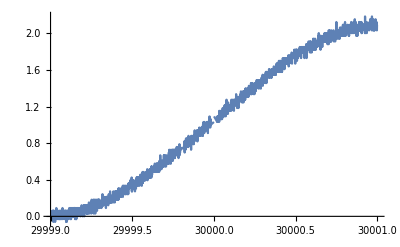

```mathematica
(*Original parametrization, numerical instability at large r*)
k2[b_,r_]:=((1-(b-r))(1+(b-r)))/(4 b r);
ξ[b_,r_]:=2b r(4-7 r^2-b^2);

EK[b_,r_]:=EllipticK[k2[b,r]];
EE[b_,r_]:=EllipticE[k2[b,r]];
EP[b_,r_]:=3(b-r)EllipticPi[k2[b,r](b+r)^2,k2[b,r]];
ΛOrig[b_,r_]:=((((r+b)^2-1)/(r+b))(-2r(2(r+b)^2+(r+b)(r-b)-3)EK[b,r]+EP[b,r])-2ξ[b,r] EE[b,r])/(9π √(b r));
s2Orig[b_,r_]:=(2π)/3(1-3/2 ΛOrig[b,r]-HeavisideTheta[r-b]);
With[{r=3 10^4},Plot[s2Orig[b,r],{b,r-1,r+1}]]
```

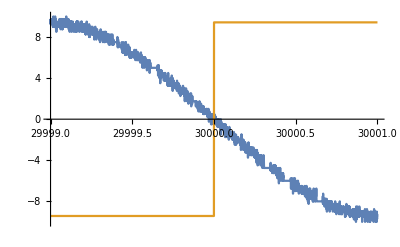

```mathematica
(*Rewritten to focus on the term causing the instability*)
k2[b_,r_]:=((1-(b-r))(1+(b-r)))/(4 b r);
ξ[b_,r_]:=2b r(4-7 r^2-b^2);

EK[b_,r_]:=EllipticK[k2[b,r]];
EE[b_,r_]:=EllipticE[k2[b,r]];
EP[b_,r_]:=3(b-r)EllipticPi[k2[b,r](b+r)^2,k2[b,r]];(*OK but can be improved*)
Λ[b_,r_]:=((((r+b)^2-1)/(r+b))(-2r(2(r+b)^2+(r+b)(r-b)-3)))/(9π √(b r))EK[b,r]+(((r+b)^2-1)/(r+b))/(9π √(b r))EP[b,r]-(2ξ[b,r])/(9π √(b r))EE[b,r];
f[b_,r_]:=√(b/r)+√(r/b)-1/(√(b r)(b+r));
BadTerm[b_,r_]:=f[b,r](-2r(2(r+b)^2+(r+b)(r-b)-3))EK[b,r]-(2ξ[b,r])/(√(b r))EE[b,r];
GoodTerm[b_,r_]:=f[b,r]EP[b,r];
Λ[b_,r_]:=1/(9π)(BadTerm[b,r]+GoodTerm[b,r]);
s2[b_,r_]:=(2π)/3(1-3/2 Λ[b,r]-HeavisideTheta[r-b]);
With[{r=3 10^4},Plot[{BadTerm[b,r], GoodTerm[b,r]},{b,r-1,r+1}]]
```

```mathematica
(*The problematic term is*)
BadTerm[b,r]
```

-(4 b r (4-b^2-7 r^2) EllipticE[((1+b-r) (1-b+r))/(4 b r)])/(√(b r))-2 r (√(b/r)+√(r/b)-1/(√(b r) (b+r))) (-3+(-b+r) (b+r)+2 (b+r)^2) EllipticK[((1+b-r) (1-b+r))/(4 b r)]

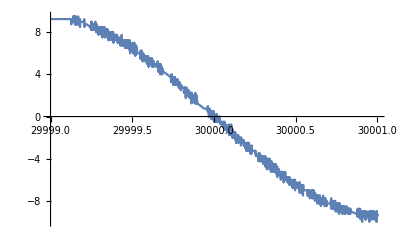

```mathematica
(*Rodrigo's original parametrization*)
k2[b_,r_]:=((1-(b-r))(1+(b-r)))/(4 b r);
ξ[b_,r_]:=2b r(4-7 r^2-b^2);

EK[b_,r_]:=EllipticK[k2[b,r]];
EE[b_,r_]:=EllipticE[k2[b,r]];
EP[b_,r_]:=EllipticPi[1-1/(b-r)^2,k2[b,r]];
CoeffK[b_,r_]:=(-3-2 r (b^3+5 b^2 r+3 r (-2+r^2)+b (-4+7 r^2)))/(√(b r));
CoeffE[b_,r_]:=(-(-4 b r (-4+b^2+7 r^2)))/(√(b r));
BadTerm[b_,r_]:=CoeffK[b,r] EK[b,r]+CoeffE[b,r] EE[b,r];
GoodTerm[b_,r_]:=(3((b+r)/(b-r))EP[b,r])/(√(b r));
Λ[b_,r_]:=(BadTerm[b,r]+GoodTerm[b,r])/(9π);
s2[b_,r_]:=(2π)/3(1-3/2 Λ[b,r]-HeavisideTheta[r-b]);
With[{r=3 10^4},Plot[BadTerm[b,r],{b,r-1,r+1}]]
```

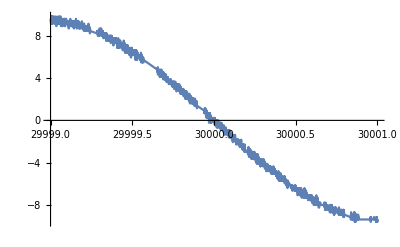

```mathematica
(*A sad attempt*)
k2[b_,r_]:=((1-(b-r))(1+(b-r)))/(4 b r);
ξ[b_,r_]:=2b r(4-7 r^2-b^2);

EK[b_,r_]:=EllipticK[k2[b,r]];
EE[b_,r_]:=EllipticE[k2[b,r]];
EP[b_,r_]:=EllipticPi[1-1/(b-r)^2,k2[b,r]];
CoeffK[b_,r_]:=8 -2 b^2 -3/(b r)+(12 r)/b-10 b r -14 r^2 -(6 r^3)/b;
CoeffE[b_,r_]:=-16 +4 b^2 +28 r^2 ;
BadTerm[b_,r_]:=√(b r)(CoeffK[b,r] EK[b,r]+CoeffE[b,r] EE[b,r]);
GoodTerm[b_,r_]:=(3((b+r)/(b-r))EP[b,r])/(√(b r));
Λ[b_,r_]:=(BadTerm[b,r]+GoodTerm[b,r])/(9π);
s2[b_,r_]:=(2π)/3(1-3/2 Λ[b,r]-HeavisideTheta[r-b]);
With[{r=3 10^4},Plot[BadTerm[b,r],{b,r-1,r+1}]]
```

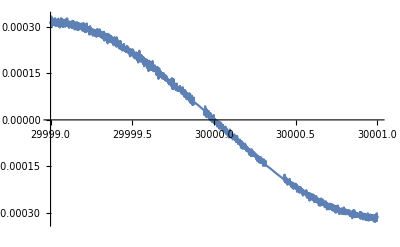

```mathematica
With[{r=3 10^4},Plot[
b^2((-2 -10 ( r/b) -14 (r/b)^2 -6(r/b)^3)EK[b,r]+(4 +28 (r/b)^2 )EE[b,r])+
 ( 8EK[b,r]-16EE[b,r]-3/(b r)EK[b,r]+12(r/b)EK[b,r])
,{b,r-1,r+1}]]
```

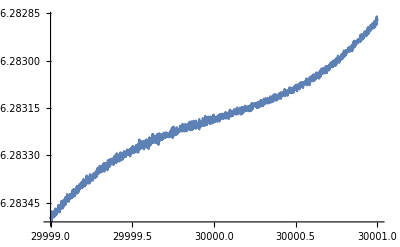

```mathematica
With[{r=3 10^4},Plot[
b^2((-2 -10 ( r/b) -14 (r/b)^2 -6(r/b)^3)EK[b,r]+(4 +28 (r/b)^2 )EE[b,r])
,{b,r-1,r+1}]]
```

```mathematica
(*
b/r=(1+ϵ);
r/b=(1-ϵ);
ϵ=1-r/b=(b-r)/b
*)
Collect[((-2 -10(1-ϵ) -14 (1-ϵ)^2 -6(1-ϵ)^3)EK+(4 +28 (1-ϵ)^2 )EE),ϵ]
```

32 EE-32 EK+(-56 EE+56 EK) ϵ+(28 EE-32 EK) ϵ^2+6 EK ϵ^3

```mathematica
32( EE- EK)-56(EE-EK) ϵ+4(7 EE-8 EK) ϵ^2+6 EK ϵ^3
```

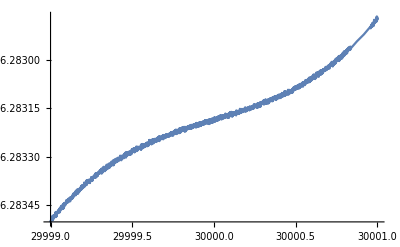

```mathematica
With[{r=3 10^4},Plot[
(32 b^2( EE[b,r]- EK[b,r])-56b(EE[b,r]-EK[b,r])(b-r)+4(7 EE[b,r]-8 EK[b,r]) (b-r)^2+(6 EK[b,r](b-r)^3)/b)
,{b,r-1,r+1}]]
```

```mathematica
Normal[Series[EllipticE[ksq],{ksq,0,1}]]-Normal[Series[EllipticK[ksq],{ksq,0,1}]]
7Normal[Series[EllipticE[ksq],{ksq,0,1}]]-8Normal[Series[EllipticK[ksq],{ksq,0,1}]]
```

-(ksq π)/4

```mathematica
FullSimplify[7 (π/2-(ksq π)/8)-8 (π/2+(ksq π)/8)]
```

-1/8 (4+15 ksq) π

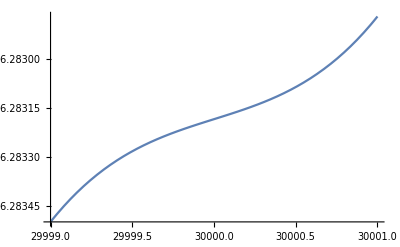

```mathematica
With[{r=3 10^4},Plot[
(32 b^2( -π/4 k2[b,r])-56b(-π/4 k2[b,r])(b-r)+4(-1/8 (4+15 k2[b,r]) π) (b-r)^2+(6 EK[b,r](b-r)^3)/b)
,{b,r-1,r+1}]]
```

```mathematica
With[{r=3 10^4},Plot[
(-8π k2[b,r] b^2+14π k2[b,r]b(b-r)-π/2( 4+15 k2[b,r]) (b-r)^2+(6(π/2+π/8 k2[b,r])(b-r)^3)/b)
,{b,r-1,r+1}]]
```

-Graphics-

```mathematica
With[{r=3 10^4},Plot[(
-2π (1-(b-r))(1+(b-r))(b/r)
+(7π)/2 (1-(b-r))(1+(b-r))(b/r-1)
-π/2( 4+15 ((1-(b-r))(1+(b-r)))/(4 b r)) (b-r)^2
+(6(π/2+π/8((1-(b-r))(1+(b-r)))/(4 b r))(b-r)^3)/b
),{b,r-1,r+1}]]
```

-Graphics-

```mathematica
With[{r=3 10^4},Plot[
-π/8 (1-(b-r))(1+(b-r)) (b/r)
-(9π)/8 (1-(b-r))(1+(b-r)) (r/b)
+π(b-r)^2
-3π(b-r)^2(r/b)
-π/2(1-(b-r))(1+(b-r))
-π/4(1-(b-r))(1+(b-r))(r/b)(r/b)
,{b,r-1,r+1}]]
```

-Graphics-

```mathematica
ζ[b_,r_]:=Module[{x=b-r,y=b/r,z},
z=(1-x)(1+x);
π/8(x^2(8-24/y)-z( y+4+9/y+2/y^2))
];
With[{r=3 10^4},Plot[ζ[b,r],{b,r-1,r+1}]]
```

-Graphics-

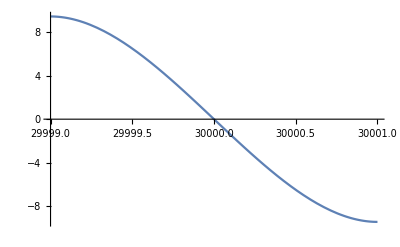

```mathematica
With[{r=3 10^4},Plot[√(b r)(ζ[b,r]+ ( 8EK[b,r]-16EE[b,r]-3/(b r)EK[b,r]+12(r/b)EK[b,r])),{b,r-1,r+1}]]
```

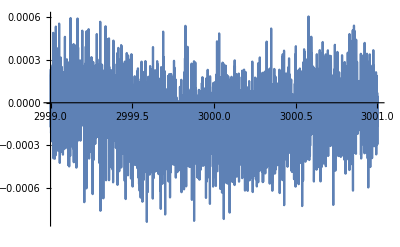

```mathematica
Z[b_,r_]:=Module[{x=b-r,y=b/r,z,ζ},
z=(1-x)(1+x);
ζ=π/8(x^2(8-24/y)-z( y+4+9/y+2/y^2));
√(b r)(ζ+ 8EK[b,r]-16EE[b,r]-3/(b r)EK[b,r]+12/y EK[b,r])
];
With[{r=3 10^3},Plot[{BadTerm[b,r]-Z[b,r]},{b,r-1,r+1}]]
```

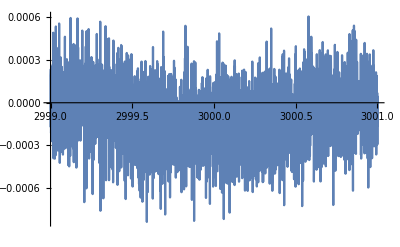

```mathematica
Z[b_,r_]:=Module[{x=b-r,y=b/r,z},
z=(1-x)(1+x);
π/8 √(b r)(-32+8 x^2(1-3/y)-z( y+4+9/y+2/y^2)+48/y+ (3(3z-4))/b^2)
];
With[{r=3 10^3},Plot[{BadTerm[b,r]-Z[b,r]},{b,r-1,r+1}]]
```

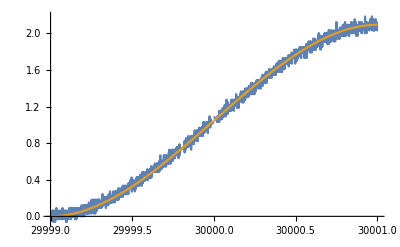

```mathematica
(*Final parametrization, stable at large r but only **linear** in accuracy*)
Λ[b_,r_]:=Module[{x=b-r,y=b/r,z},
z=(1-x)(1+x);
1/72 √(b r)(-32+8 x^2(1-3/y)-z( y+4+9/y+2/y^2)+48/y+ (3(3z-4))/b^2)+((x √y+x/(√y)-x/(2 b^2)) EllipticPi[z(1/2+y/4+1/(4y)),z/(4 b^2)])/(3π)
];
s2[b_,r_]:=(2π)/3(1-3/2 Λ[b,r]-HeavisideTheta[r-b]);
With[{r=3 10^4},Plot[{s2Orig[b,r],s2[b,r]},{b,r-1,r+1}]]
```

```mathematica
(*Final parametrization, stable at large r but only **linear** in accuracy*)
```

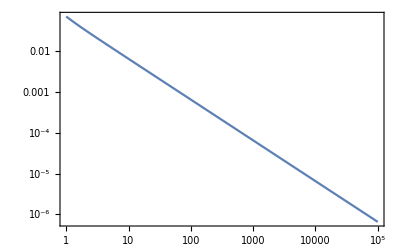

```mathematica
LogLogPlot[s2Orig[SetAccuracy[r,30],SetAccuracy[r+0.01,30]]-s2[r,r+0.01],{r,1,10^5},Frame->True,GridLines->Automatic]
```

For r = 100, where we are currently having trouble, the max error is at the ppt level. We should be able to do better than this. 

Let’s re-derive the math using a 3rd order expansion for the elliptic integrals...

```mathematica
((32 b^2( EE- EK)-56b(EE-EK)(b-r)+4(7 EE-8 EK) (b-r)^2+(6 EK(b-r)^3)/b)/.{EK->Normal[Series[EllipticK[ksq],{ksq,0,3}]],EE->Normal[Series[EllipticE[ksq],{ksq,0,3}]]})/.{ksq->k2[b,r]}
```

32 b^2 (-(π (1+b-r) (1-b+r))/(16 b r)-(3 π (1+b-r)^2 (1-b+r)^2)/(512 b^2 r^2)-(15 π (1+b-r)^3 (1-b+r)^3)/(16384 b^3 r^3))-56 b (b-r) (-(π (1+b-r) (1-b+r))/(16 b r)-(3 π (1+b-r)^2 (1-b+r)^2)/(512 b^2 r^2)-(15 π (1+b-r)^3 (1-b+r)^3)/(16384 b^3 r^3))+(6 (b-r)^3 (π/2+(π (1+b-r) (1-b+r))/(32 b r)+(9 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)+(25 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3)))/b+4 (b-r)^2 (7 (π/2-(π (1+b-r) (1-b+r))/(32 b r)-(3 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)-(5 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3))-8 (π/2+(π (1+b-r) (1-b+r))/(32 b r)+(9 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)+(25 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3)))

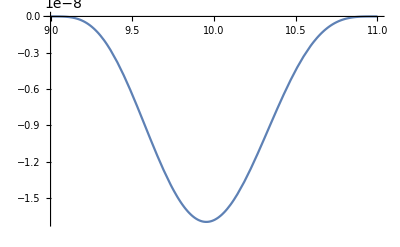

```mathematica
ProblemTerm[b_,r_]:=(32 b^2( EE[b,r]- EK[b,r])-56b(EE[b,r]-EK[b,r])(b-r)+4(7 EE[b,r]-8 EK[b,r]) (b-r)^2+(6 EK[b,r](b-r)^3)/b);
ProblemTermTaylor3[b_,r_]:=32 b^2 (-(π (1+b-r) (1-b+r))/(16 b r)-(3 π (1+b-r)^2 (1-b+r)^2)/(512 b^2 r^2)-(15 π (1+b-r)^3 (1-b+r)^3)/(16384 b^3 r^3))-56 b (b-r) (-(π (1+b-r) (1-b+r))/(16 b r)-(3 π (1+b-r)^2 (1-b+r)^2)/(512 b^2 r^2)-(15 π (1+b-r)^3 (1-b+r)^3)/(16384 b^3 r^3))+(6 (b-r)^3 (π/2+(π (1+b-r) (1-b+r))/(32 b r)+(9 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)+(25 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3)))/b+4 (b-r)^2 (7 (π/2-(π (1+b-r) (1-b+r))/(32 b r)-(3 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)-(5 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3))-8 (π/2+(π (1+b-r) (1-b+r))/(32 b r)+(9 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)+(25 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3)))
With[{r=10},Plot[{ProblemTerm[SetAccuracy[b,30],SetAccuracy[r,30]]-ProblemTermTaylor3[b,r]},{b,r-1,r+1}]]
```

BOOM. That seems like enough!

## THE SOLUTION

```mathematica
((b^2((-2 -10 ( r/b) -14 (r/b)^2 -6(r/b)^3)EK+(4 +28 (r/b)^2 )EE))/.{EK->Normal[Series[EllipticK[ksq],{ksq,0,3}]],EE->Normal[Series[EllipticE[ksq],{ksq,0,3}]]})/.{ksq->k2[b,r]}
```

b^2 ((4+(28 r^2)/b^2) (π/2-(π (1+b-r) (1-b+r))/(32 b r)-(3 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)-(5 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3))+(-2-(10 r)/b-(14 r^2)/b^2-(6 r^3)/b^3) (π/2+(π (1+b-r) (1-b+r))/(32 b r)+(9 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)+(25 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3)))

```mathematica
ProblemTermTaylor3[b_,r_]:=b^2 ((4+(28 r^2)/b^2) (π/2-(π (1+b-r) (1-b+r))/(32 b r)-(3 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)-(5 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3))+(-2-(10 r)/b-(14 r^2)/b^2-(6 r^3)/b^3) (π/2+(π (1+b-r) (1-b+r))/(32 b r)+(9 π (1+b-r)^2 (1-b+r)^2)/(2048 b^2 r^2)+(25 π (1+b-r)^3 (1-b+r)^3)/(32768 b^3 r^3)))
```

```mathematica
Z[b_,r_]:=√(b r)(ProblemTermTaylor3[b,r]+ 8EK[b,r]-16EE[b,r]-3/(b r)EK[b,r]+12/(b/r)EK[b,r])
```

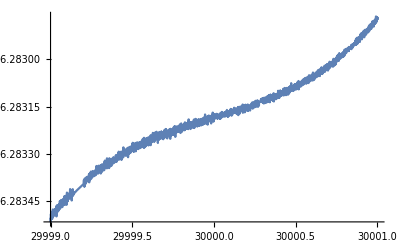

```mathematica
With[{r=3 10^4},Plot[{ProblemTermTaylor3[b,r]},{b,r-1,r+1}]]
```

That failed. Might need to go back to where we wrote b in terms of epsilon and do that to higher order!